### Start choosing the example:

```mathematica
t=9;
beta =1;
A=.5;
Get["/Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m"]
g[x]
```

x

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->2,I2->3,U1->5}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.064018,<|u1→12,u2→10,u3→10,u4→5,u5→13,u6→10,u7→5,u8→5,u9→12,u10→12,u11→13,u12→13,j1→0,j2→2,j3→0,j4→5,j5→0,j6→3,j7→0,j8→5,j9→0,j10→2,j11→0,j12→3|>}

### Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1->2,I2->3,U1->5}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→38059482899/5000000000,u2→15322657149/2500000000,u3→15322657149/2500000000,u4→5,u5→15322657149/2500000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→38059482899/5000000000,u12→38059482899/5000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→77491808883/10000000000,u2→60738049571/10000000000,u3→60738049571/10000000000,u4→5,u5→60738049571/10000000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→77491808883/10000000000,u12→77491808883/10000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→85493471337/10000000000,u2→58974978013/10000000000,u3→58974978013/10000000000,u4→5,u5→58974978013/10000000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→85493471337/10000000000,u12→85493471337/10000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→41/4,u2→23/4,u3→23/4,u4→5,u5→23/4,u6→5,u7→5,u8→5,u9→5,u10→5,u11→41/4,u12→41/4,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[jt859]&&NonNegative[2-jt859]&&NonNegative[2-jt859]&&NonNegative[-2+jt859]&&NonNegative[-2+jt859]&&NonNegative[5-jt859]&&NonNegative[12-u869]&&NonNegative[-1-u869+u871]&&NonNegative[-12+u869]&&NonNegative[-13+u871]&&NonNegative[1+u869-u871]&&NonNegative[13-u871]&&(jt859==0||2-jt859==0)&&(2-jt859==0||-2+jt859==0)&&(-2+jt859==0||5-jt859==0)&&(jt859==0||12-u869==0)&&(2-jt859==0||-1-u869+u871==0)&&(2-jt859==0||-12+u869==0)&&(-2+jt859==0||-13+u871==0)&&(-2+jt859==0||1+u869-u871==0)&&(5-jt859==0||13-u871==0)
and the rules are:
<|j845→2,j846→5,j847→3,j848→5,j849→2,j850→3,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,jt857→0,jt858→2,jt860→2-jt859,jt861→2-jt859,jt862→-2+jt859,jt863→-2+jt859,jt864→5-jt859,jt865→0,jt866→3,jt867→5,jt868→0,u872→5,u875→-2+u869,u876→-5+10,u877→-3+u871,u878→5,u879→u869,u880→u871,u870→10,u873→u869,u874→u871|>

DataToEquations: It took 0.006002 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
jt859==2&&u869==12&&u871==13
and the rules are:
<|j845→2,j846→5,j847→3,j848→5,j849→2,j850→3,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,jt857→0,jt858→2,jt860→2-jt859,jt861→2-jt859,jt862→-2+jt859,jt863→-2+jt859,jt864→5-jt859,jt865→0,jt866→3,jt867→5,jt868→0,u872→5,u875→-2+u869,u876→-5+10,u877→-3+u871,u878→5,u879→u869,u880→u871,u870→10,u873→u869,u874→u871|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j845-j851+IntM[j845-j851,1->2],j846-j852+IntM[j846-j852,2->4],j847-j853+IntM[j847-j853,3->2]}

DataToEquations: Done.

{0.025977,Null}

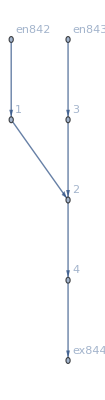

<|j845→2,j846→5,j847→3,j848→5,j849→2,j850→3,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,jt857→0,jt858→2,jt859→2,jt860→0,jt861→0,jt862→0,jt863→0,jt864→3,jt865→0,jt866→3,jt867→5,jt868→0,u869→12,u870→10,u871→13,u872→5,u873→12,u874→13,u875→10,u876→5,u877→10,u878→5,u879→12,u880→13|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,I2->3,U1->5}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
d2e=D2E[Data/.{I1->2,I2->3,U1->5}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduce2[d2e=D2E[Data/.{I1->2,I2->3,U1->5}]],<||>,1]//KeySort
KeySort@<|u1->12,u2->10,u3->10,u4->5,u5->13,u6->10,u7->5,u8->5,u9->12,u10->12,u11->13,u12->13,j1->0,j2->2,j3->0,j4->5,j5->0,j6->3,j7->0,j8->5,j9->0,j10->2,j11->0,j12->3|>
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

{u1==12&&u10==12&&u11==13,True,True,True,True,True,True,True,True,u1==u10,u1==-1+u11,True}

{True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Done!

<|j1→0,j10→2,j11→0,j12→3,j2→2,j3→0,j4→5,j5→0,j6→3,j7→0,j8→5,j9→0,u1→12,u10→12,u11→13,u12→13,u2→10,u3→10,u4→5,u5→13,u6→10,u7→5,u8→5,u9→12|>

<|j1→0,j10→2,j11→0,j12→3,j2→2,j3→0,j4→5,j5→0,j6→3,j7→0,j8→5,j9→0,u1→12,u10→12,u11→13,u12→13,u2→10,u3→10,u4→5,u5→13,u6→10,u7→5,u8→5,u9→12|>

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1->2,I2->3,U1->5}];
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

{u1==12&&u10==12&&u11==13,True,True,True,True,True,True,True,True,u1==u10,u1==-1+u11,True}

{True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Done!

EliminateVarsSimplify for the us

{u1==12&&u10==12&&u11==13,True,True,True,True,True,True,True,True,u1==u10,u1==-1+u11,True}

{True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Done!

<|u1→12,u2→10,u3→10,u4→5,u5→13,u6→10,u7→5,u8→5,u9→12,u10→12,u11→13,u12→13,j1→0,j2→2,j3→0,j4→5,j5→0,j6→3,j7→0,j8→5,j9→0,j10→2,j11→0,j12→3|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.48524&&j15-j21-u39+u45==2.79084&&j16-j22-u40+u46==1.20564

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.16375×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==0.48524&&j15-j21-u39+u45==2.79084&&j16-j22-u40+u46==1.20564

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.16375×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→8.72392,u39→7.20916,u40→9.00353,u41→5,u42→8.72392,u43→9.00353,u44→7.20916,u45→5,u46→7.20916,u47→5,u48→8.72392,u49→9.00353|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.412423&&j15-j21-u39+u45==2.46832&&j16-j22-u40+u46==1.04398

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.37632×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==0.412423&&j15-j21-u39+u45==2.46832&&j16-j22-u40+u46==1.04398

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.37632×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→9.11925,u39→7.53168,u40→9.48769,u41→5,u42→9.11925,u43→9.48769,u44→7.53168,u45→5,u46→7.53168,u47→5,u48→9.11925,u49→9.48769|>

```mathematica
alpha = 0.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.324624&&j15-j21-u39+u45==2.03779&&j16-j22-u40+u46==0.840074

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.81892×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==0.324624&&j15-j21-u39+u45==2.03779&&j16-j22-u40+u46==0.840074

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.81892×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→9.63758,u39→7.96221,u40→10.1221,u41→5,u42→9.63758,u43→10.1221,u44→7.96221,u45→5,u46→7.96221,u47→5,u48→9.63758,u49→10.1221|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.081441&&j15-j21-u39+u45==0.582451&&j16-j22-u40+u46==0.223572

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.15513×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==0.081441&&j15-j21-u39+u45==0.582451&&j16-j22-u40+u46==0.223572

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.15513×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→11.3361,u39→9.41755,u40→12.194,u41→5,u42→11.3361,u43→12.194,u44→9.41755,u45→5,u46→9.41755,u47→5,u48→11.3361,u49→12.194|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j845-j851-u869+u875==0&&j846-j852-u870+u876==0&&j847-j853-u871+u877==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[6.77873×10^-15,ComplexInfinity]

<|j845→2,j846→5,j847→3,j848→5,j849→2,j850→3,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,jt857→0,jt858→2,jt859→2,jt860→0,jt861→0,jt862→0,jt863→0,jt864→3,jt865→0,jt866→3,jt867→5,jt868→0,u869→12,u870→10,u871→13,u872→5,u873→12,u874→13,u875→10,u876→5,u877→10,u878→5,u879→12,u880→13|>

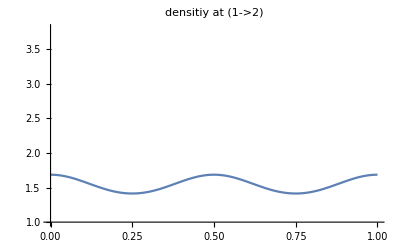
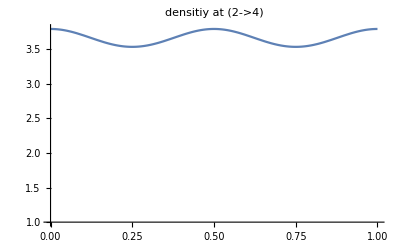
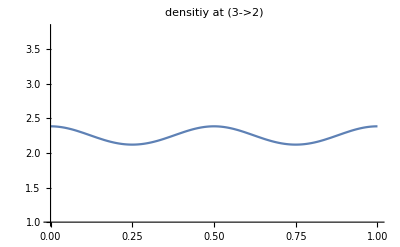

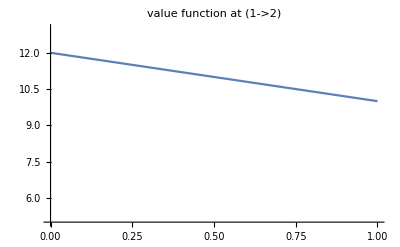
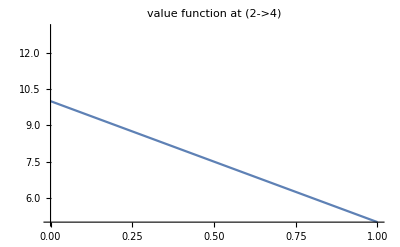
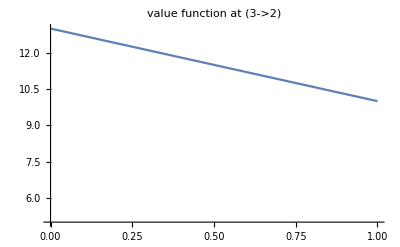

```mathematica
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#,PlotRange->{1,3.8}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#,PlotRange-> {5,13}]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==-0.200829&&j15-j21-u39+u45==-1.66505&&j16-j22-u40+u46==-0.588344

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.49865×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==-0.200829&&j15-j21-u39+u45==-1.66505&&j16-j22-u40+u46==-0.588344

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.49865×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→13.8659,u39→11.665,u40→15.2534,u41→5,u42→13.8659,u43→15.2534,u44→11.665,u45→5,u46→11.665,u47→5,u48→13.8659,u49→15.2534|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==-0.651849&&j15-j21-u39+u45==-6.78347&&j16-j22-u40+u46==-2.10421

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.3531×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==-0.651849&&j15-j21-u39+u45==-6.78347&&j16-j22-u40+u46==-2.10421

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.3531×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→19.4353,u39→16.7835,u40→21.8877,u41→5,u42→19.4353,u43→21.8877,u44→16.7835,u45→5,u46→16.7835,u47→5,u48→19.4353,u49→21.8877|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==-0.867277&&j15-j21-u39+u45==-10.0199&&j16-j22-u40+u46==-2.92473

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.39846×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==-0.867277&&j15-j21-u39+u45==-10.0199&&j16-j22-u40+u46==-2.92473

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.39846×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→22.8872,u39→20.0199,u40→25.9446,u41→5,u42→22.8872,u43→25.9446,u44→20.0199,u45→5,u46→20.0199,u47→5,u48→22.8872,u49→25.9446|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==-1.47148&&j15-j21-u39+u45==-22.4774&&j16-j22-u40+u46==-5.56607

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.06136×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==-1.47148&&j15-j21-u39+u45==-22.4774&&j16-j22-u40+u46==-5.56607

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.06136×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→35.9489,u39→32.4774,u40→41.0435,u41→5,u42→35.9489,u43→41.0435,u44→32.4774,u45→5,u46→32.4774,u47→5,u48→35.9489,u49→41.0435|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==-1.91028&&j15-j21-u39+u45==-35.2988&&j16-j22-u40+u46==-7.80509

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.15727×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==-1.91028&&j15-j21-u39+u45==-35.2988&&j16-j22-u40+u46==-7.80509

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.15727×10^-16

<|j14→2,j15→5,j16→3,j17→5,j18→2,j19→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→2,jt29→0,jt30→0,jt31→0,jt32→0,jt33→3,jt34→0,jt35→3,jt36→5,jt37→0,u38→49.209,u39→45.2988,u40→56.1039,u41→5,u42→49.209,u43→56.1039,u44→45.2988,u45→5,u46→45.2988,u47→5,u48→49.209,u49→56.1039|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j845-j851-u869+u875==-2.5&&j846-j852-u870+u876==-58.75&&j847-j853-u871+u877==-11.25

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89983×10^-16

FRX1: nonlinear: 
j845-j851-u869+u875==-2.5&&j846-j852-u870+u876==-58.75&&j847-j853-u871+u877==-11.25

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89983×10^-16

<|j845→2,j846→5,j847→3,j848→5,j849→2,j850→3,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,jt857→0,jt858→2,jt859→2,jt860→0,jt861→0,jt862→0,jt863→0,jt864→3,jt865→0,jt866→3,jt867→5,jt868→0,u869→73.25,u870→68.75,u871→83.,u872→5,u873→73.25,u874→83.,u875→68.75,u876→5,u877→68.75,u878→5,u879→73.25,u880→83.|>

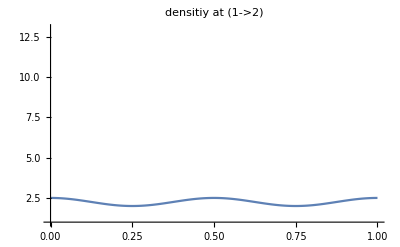
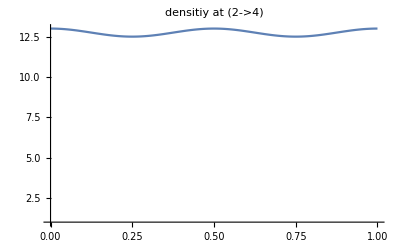
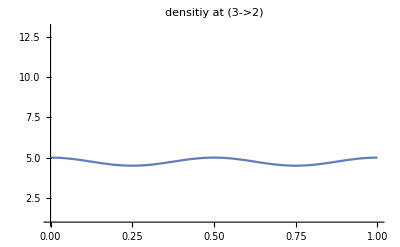

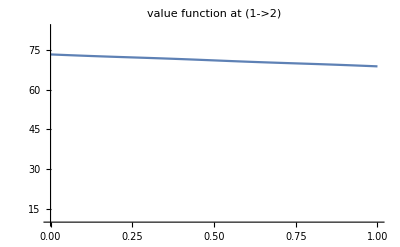
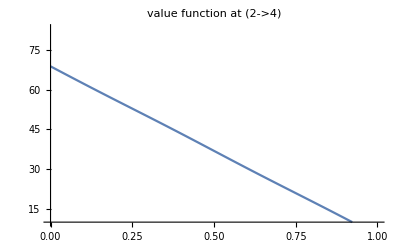
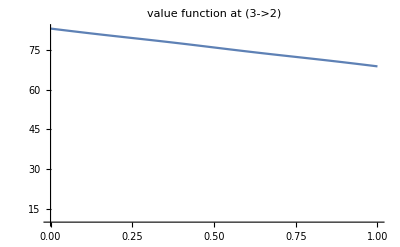

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#,PlotRange->{1,13}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#,PlotRange->{10,83}]&/@MFGEquations["BEL"]
```

#### Plots

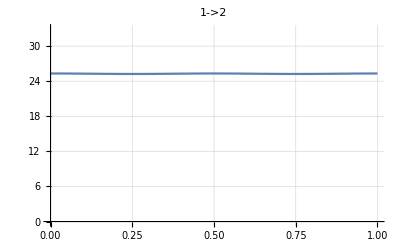
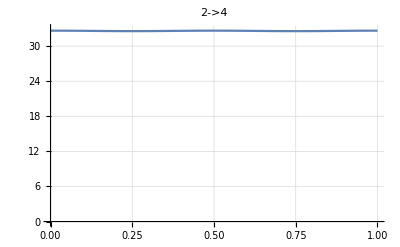
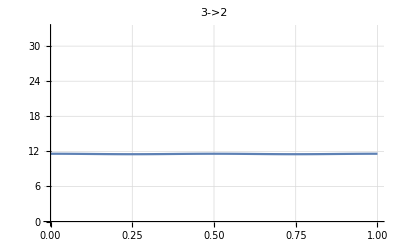

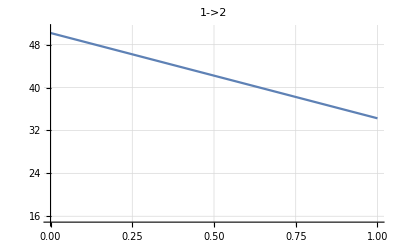
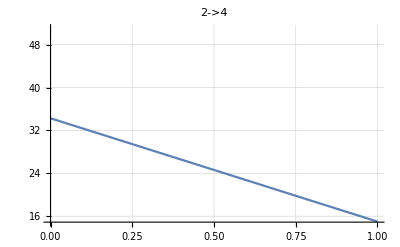
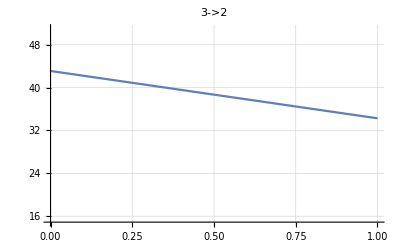

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,33},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{15-0.1,51},GridLines->Automatic]&/@MFGEquations["BEL"]
```

### Old stuff

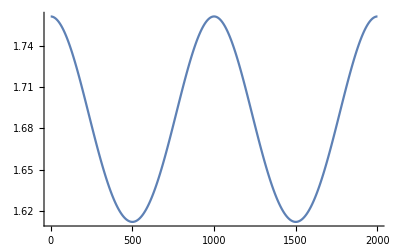
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]&/@MFGEquations["BEL"]
```

```mathematica
jv=Values[MFGEquations["jvars"]]/.FFR
```

{80,110,30,110,80,30,0,0,0,0,0,0}

```mathematica
a=1
```

1

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

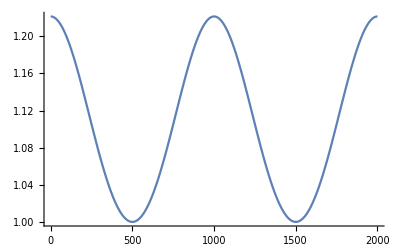
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

```mathematica
Plot[{0,Values[(mfunc[#])/.JTJNZ]},{x,0,1},PlotLabel->"m"#]&/@BEL
Plot[Join[Last/@Data["Exit Vertices and Terminal Costs"],Values[(ufunc[#])/.Join[JTJNZ,URNZ]]],{y,0,1},PlotLabel->"u"#]&/@BEL
```

### Ricardo’s input

the way we use some functions has changed, we need to provide the edge (or anything, for now)

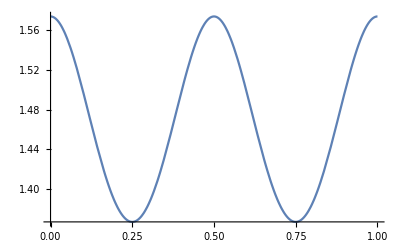

```mathematica
Plot[M[1,x,edge],{x,0,1}]
```

```mathematica
jv=Values[MFGEquations["jvars"]]/.FFR
```

{80,110,30,110,80,30,0,0,0,0,0,0}

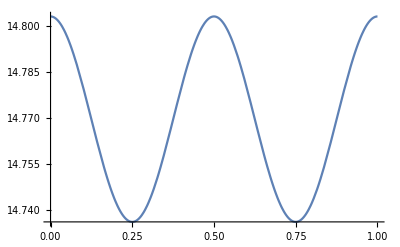
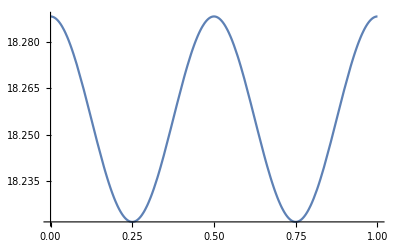
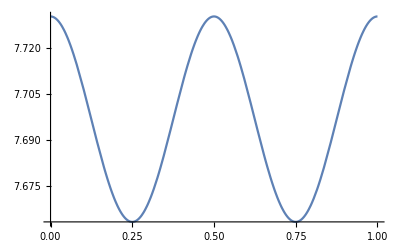
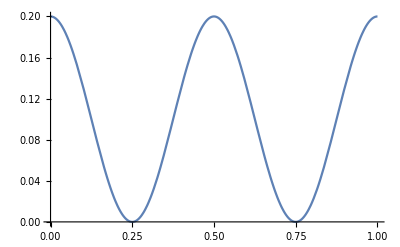
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[M[#,x,edge],{x,0,1}]&/@jv
```

```mathematica
jv=jv//DeleteDuplicates
```

{80,110,30,0}

```mathematica
Plot[M[#,x,edge],{x,0,1}]&/@jv
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}